# Ising /QUBO formulation for Chemical Computation

#### Abhishek Sharma Cronin Lab University of Glasgow abhishek.sharma@glasgow.ac.uk

```mathematica
baseDirectory=NotebookDirectory[]
```

/Volumes/scapa4/group/0-Papers Published/2024/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/GitHub_Repo/BZ_Mappings/

## Scaling of quadratic couplings with number of input variables

```mathematica
nComb[nVar_]:=Block[{nX},nX=Table[Symbol["x"<>ToString[i]],{i,nVar}];Length@DeleteDuplicates[Tuples[nX,2],Sort@#1==Sort@#2&]]
```

```mathematica
nCouplings=Table[{n,nComb[n]},{n,1,100,10}];
```

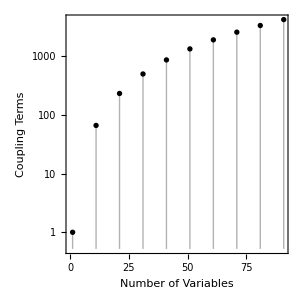

```mathematica
ListLogPlot[nCouplings,PlotStyle-> Black,Filling-> Axis,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame-> True,AspectRatio->1,FrameLabel->{"Number of Variables","Coupling Terms"},ImageSize->300]
```

## 4-variable QUBO Mapping on BZ Platform : Full Connectivity

```mathematica
nVar=4; (* Number of variables *)
```

```mathematica
nX=Table[Symbol["x"<>ToString[i]],{i,nVar}]; (* Variables List *)
```

```mathematica
comb=DeleteDuplicates[Tuples[nX,2],Sort@#1==Sort@#2&]; (* Fully connected variable combinations *)
```

```mathematica
combCoeff=DeleteDuplicates[Tuples[Range[nVar],2],Sort@#1==Sort@#2&]; (* Fully connected sets with self interaction *)
```

```mathematica
coeffs=("C"<>ToString[#⟦1⟧]<>ToString[#⟦2⟧])&/@combCoeff; (* Coefficient List for connection variables *)
```

The Hamiltonian for fully connected four variable problem looks like,

```mathematica
quadTerms=#⟦1⟧#⟦2⟧&/@comb;
HamQUBO=coeffs.quadTerms
```

C11 x1^2+C12 x1 x2+C22 x2^2+C13 x1 x3+C23 x2 x3+C33 x3^2+C14 x1 x4+C24 x2 x4+C34 x3 x4+C44 x4^2

```mathematica
MapThread[(#1⟦1⟧<->#1⟦2⟧-> #2)&,{comb,coeffs}]
```

{x1<->x1→C11,x1<->x2→C12,x1<->x3→C13,x1<->x4→C14,x2<->x2→C22,x2<->x3→C23,x2<->x4→C24,x3<->x3→C33,x3<->x4→C34,x4<->x4→C44}

```mathematica
out=Graph[#⟦1⟧-> #⟦2⟧&/@comb,EdgeLabels->MapThread[(#1⟦1⟧<->#1⟦2⟧-> Placed[#2,0.4])&,{comb,coeffs}],EdgeLabelStyle->Directive[Black,16,Background-> White],PlotTheme->"Scientific",DirectedEdges->False,GraphLayout->"GridEmbedding",VertexShapeFunction->"Square",VertexSize->{0.1,0.1}, VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[White,Bold,FontFamily->"Arial",16]]
```

-Graphics-

```mathematica
Export[baseDirectory<>"out_4var.png",out,ImageResolution->300]
```

/Volumes/scapa4/group/0-Papers Published/2024/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/GitHub_Repo/BZ_Mappings/out_4var.png

```mathematica
Export[baseDirectory<>"out_4var.svg",out]
```

/Volumes/scapa4/group/0-Papers Published/2024/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/GitHub_Repo/BZ_Mappings/out_4var.svg

To map fully connected 4 variable problem on BZ platform, we need additional cells for self interaction and complex coupling which are not possible with nearest neighbours.

```mathematica
nXSI=Table[Symbol["x"<>ToString[i]],{i,nVar}]; (* Self Interaction Cells name *)
```

```mathematica
nXAUX=Symbol["x"<>ToString[#]]&/@{4,3,2,1} ;(* Auxiliary Cells Name *)
```

```mathematica
nXX=ConstantArray["X",4]; (* Unused Cells Name *)
```

We need 12 connected BZ cells where four cells correspond to interacting cells, four cells for self interactions each and four auxiliary cells for full connecting mapping on two dimensional rectangular grid. This is relatively simpler case, so we can define the cells ourselves.

```mathematica
cellsQUBO={{2,2},{2,3},{3,2},{3,3}};
cellsSI={{2,1}, {2,4}, {3,1}, {3,4}};
cellsAUX={{1,2}, {1,3},{4,2}, {4,3}};
cellsX={{1,1}, {1,4},{4,1},{4,4}};
```

```mathematica
matSizeX=4;matSizeY=4;
cellsType=ConstantArray[-1,{matSizeX,matSizeY}]; (* Cells Type *)
Table[cellsType⟦cellsQUBO⟦i,1⟧,cellsQUBO⟦i,2⟧⟧=0,{i,Length[cellsQUBO]}];
Table[cellsType⟦cellsSI⟦i,1⟧,cellsSI⟦i,2⟧⟧=1,{i,Length[cellsSI]}];
Table[cellsType⟦cellsAUX⟦i,1⟧,cellsAUX⟦i,2⟧⟧=2,{i,Length[cellsAUX]}];
```

```mathematica
nameTable=ConstantArray[0,{matSizeX,matSizeY}];
Table[nameTable⟦cellsQUBO⟦i,1⟧,cellsQUBO⟦i,2⟧⟧=nX⟦i⟧,{i,Length[cellsQUBO]}];
Table[nameTable⟦cellsSI⟦i,1⟧,cellsSI⟦i,2⟧⟧=nXSI⟦i⟧,{i,Length[cellsSI]}];
Table[nameTable⟦cellsAUX⟦i,1⟧,cellsAUX⟦i,2⟧⟧=nXAUX⟦i⟧,{i,Length[cellsAUX]}];
```

```mathematica
rules=Flatten@{(cellsQUBO⟦#⟧->nX⟦#⟧)&/@Range[nVar],(cellsSI⟦#⟧->nXSI⟦#⟧)&/@Range[nVar],(cellsAUX⟦#⟧->nXAUX⟦#⟧)&/@Range[Length[nXAUX]],(cellsX⟦#⟧->nXX⟦#⟧)&/@Range[Length[nXX]]};
```

```mathematica
couplings=
{{x1,x1}-> {C11,{{2,2},{2,1}}}, 
{x1,x2}-> {C12,{{2,2},{2,3}}},
{x1,x3}-> {C13,{{2,2},{3,2}}},
{x1,x4}-> {C14,{{2,2},{1,2}}},
{x2,x2}-> {C22,{{2,3},{2,4}}},
{x2,x3}-> {C23,{{2,3},{1,3}}},
{x2,x4}-> {C24,{{2,3},{3,3}}},
{x3,x3}-> {C33,{{3,2},{3,1}}},
{x3,x4}-> {C34,{{3,2},{3,3}}},
{x4,x4}-> {C44,{{3,3},{3,4}}},
{x4,x1}-> {C41,{{3,3},{4,3}}},
{x4,x1}-> {C32,{{3,2},{4,2}}}};
```

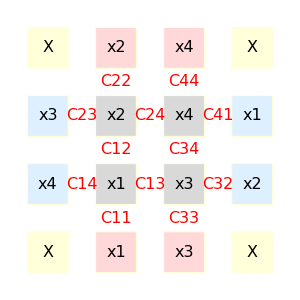

```mathematica
p1=Graphics[Flatten@{EdgeForm[Thick],LightYellow,Table[{Which[cellsType⟦i,j⟧== -1,LightYellow,cellsType⟦i,j⟧==0, LightGray,cellsType⟦i,j⟧==1, LightRed,cellsType⟦i,j⟧==2, LightBlue],Rectangle[{i-0.3,j-0.3},{i+0.3,j+0.3}]},{i,nVar},{j,nVar}],Black,Table[Text[Style[{i,j}/.rules,16],{i,j}],{i,nVar},{j,nVar}],Text[Style[couplings⟦#⟧⟦2,1⟧,16,Red],Mean[couplings⟦#⟧⟦2,2⟧]]&/@Range[Length[couplings]]},ImageSize->300]
```

```mathematica
Export[baseDirectory<>"mapping.png",p1,ImageResolution->300]
```

/Volumes/scapa4/group/0-Papers Published/2024/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/GitHub_Repo/BZ_Mappings/mapping.png

```mathematica
Export[baseDirectory<>"mapping.svg",p1]
```

/Volumes/scapa4/group/0-Papers Published/2024/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/GitHub_Repo/BZ_Mappings/mapping.svg

```mathematica
p2=SwatchLegend[{LightYellow,LightGray ,LightRed,LightBlue},{"Unused Cells","Active Cells","Self Interaction Cells","Auxiliary Cells"}]
```

```mathematica
Export[baseDirectory<>"legend.png",p2,ImageResolution->300]
```

/Volumes/scapa4/group/0-Papers Published/2024/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/GitHub_Repo/BZ_Mappings/legend.png

```mathematica
Export[baseDirectory<>"legend.svg",p2]
```

/Volumes/scapa4/group/0-Papers Published/2024/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/GitHub_Repo/BZ_Mappings/legend.svg

## 5-variable QUBO Mapping on BZ Platform : Full Connectivity

```mathematica
nVar=5; (* Number of variables *)
```

```mathematica
nX=Table[Symbol["x"<>ToString[i]],{i,nVar}]; (* Variables List *)
```

```mathematica
comb=DeleteDuplicates[Tuples[nX,2],Sort@#1==Sort@#2&]; (* Fully connected variable combinations *)
```

```mathematica
combCoeff=DeleteDuplicates[Tuples[Range[nVar],2],Sort@#1==Sort@#2&]; (* Fully connected sets with self interaction *)
```

```mathematica
coeffs=("C"<>ToString[#⟦1⟧]<>ToString[#⟦2⟧])&/@combCoeff; (* Coefficient List for connection variables *)
```

The Hamiltonian for fully connected four variable problem looks like,

```mathematica
quadTerms=#⟦1⟧#⟦2⟧&/@comb;
HamQUBO=coeffs.quadTerms
```

C11 x1^2+C12 x1 x2+C22 x2^2+C13 x1 x3+C23 x2 x3+C33 x3^2+C14 x1 x4+C24 x2 x4+C34 x3 x4+C44 x4^2+C15 x1 x5+C25 x2 x5+C35 x3 x5+C45 x4 x5+C55 x5^2

```mathematica
MapThread[(#1⟦1⟧<->#1⟦2⟧-> #2)&,{comb,coeffs}]
```

{x1<->x1→C11,x1<->x2→C12,x1<->x3→C13,x1<->x4→C14,x1<->x5→C15,x2<->x2→C22,x2<->x3→C23,x2<->x4→C24,x2<->x5→C25,x3<->x3→C33,x3<->x4→C34,x3<->x5→C35,x4<->x4→C44,x4<->x5→C45,x5<->x5→C55}

```mathematica
Graph[#⟦1⟧-> #⟦2⟧&/@comb,EdgeLabels->MapThread[(#1⟦1⟧<->#1⟦2⟧-> Placed[#2,0.3])&,{comb,coeffs}],EdgeLabelStyle->Directive[Black,12,Background-> White],PlotTheme->"Scientific",DirectedEdges->False,GraphLayout->"CircularEmbedding",VertexShapeFunction->"Square",VertexSize->{0.1,0.1}, VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[White,Bold,FontFamily->"Arial",12]]
```

-Graphics-

To map fully connected 5 variable problem on BZ platform, we need additional cells for self interaction and complex coupling which are not possible with nearest neighbours.

```mathematica
nXSI=Table[Symbol["x"<>ToString[i]],{i,nVar}]; (* Self Interaction Cells name *)
```

```mathematica
nXAUX=Symbol["x"<>ToString[#]]&/@{4,3,2,1} ;(* Auxiliary Cells Name *)
```

```mathematica
nXX=ConstantArray["X",4]; (* Unused Cells Name *)
```

We need 12 connected BZ cells where four cells correspond to interacting cells, four cells for self interactions each and four auxiliary cells for full connecting mapping on two dimensional rectangular grid. This is relatively simpler case, so we can define the cells ourselves.

```mathematica
cellsQUBO={{2,2},{2,3},{3,2},{3,3}};
cellsSI={{2,1}, {2,4}, {3,1}, {3,4}};
cellsAUX={{1,2}, {1,3},{4,2}, {4,3}};
cellsX={{1,1}, {1,4},{4,1},{4,4}};
```

## 6-variable QUBO Mapping on BZ Platform : Full Connectivity

```mathematica
nVar=6; (* Number of variables *)
```

```mathematica
nX=Table[Symbol["x"<>ToString[i]],{i,nVar}]; (* Variables List *)
```

```mathematica
comb=DeleteDuplicates[Tuples[nX,2],Sort@#1==Sort@#2&]; (* Fully connected variable combinations *)
```

```mathematica
combCoeff=DeleteDuplicates[Tuples[Range[nVar],2],Sort@#1==Sort@#2&]; (* Fully connected sets with self interaction *)
```

```mathematica
coeffs=("C"<>ToString[#⟦1⟧]<>ToString[#⟦2⟧])&/@combCoeff; (* Coefficient List for connection variables *)
```

The Hamiltonian for fully connected four variable problem looks like,

```mathematica
quadTerms=#⟦1⟧#⟦2⟧&/@comb;
HamQUBO=coeffs.quadTerms
```

C11 x1^2+C12 x1 x2+C22 x2^2+C13 x1 x3+C23 x2 x3+C33 x3^2+C14 x1 x4+C24 x2 x4+C34 x3 x4+C44 x4^2+C15 x1 x5+C25 x2 x5+C35 x3 x5+C45 x4 x5+C55 x5^2+C16 x1 x6+C26 x2 x6+C36 x3 x6+C46 x4 x6+C56 x5 x6+C66 x6^2

```mathematica
MapThread[(#1⟦1⟧<->#1⟦2⟧-> #2)&,{comb,coeffs}]
```

{x1<->x1→C11,x1<->x2→C12,x1<->x3→C13,x1<->x4→C14,x1<->x5→C15,x1<->x6→C16,x2<->x2→C22,x2<->x3→C23,x2<->x4→C24,x2<->x5→C25,x2<->x6→C26,x3<->x3→C33,x3<->x4→C34,x3<->x5→C35,x3<->x6→C36,x4<->x4→C44,x4<->x5→C45,x4<->x6→C46,x5<->x5→C55,x5<->x6→C56,x6<->x6→C66}

```mathematica
Graph[#⟦1⟧-> #⟦2⟧&/@comb,EdgeLabels->MapThread[(#1⟦1⟧<->#1⟦2⟧-> Placed[#2,0.4])&,{comb,coeffs}],EdgeLabelStyle->Directive[Black,12,Background-> White],PlotTheme->"Scientific",DirectedEdges->False,GraphLayout->"CircularEmbedding",VertexShapeFunction->"Square",VertexSize->{0.1,0.1}, VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[White,Bold,FontFamily->"Arial",12]]
```

-Graphics-